## Paths and Includes

```mathematica
SetOptions[$FrontEnd,"CommonDefaultFormatTypes"->{"Output"->StandardForm}]
```

```mathematica
basepath=$HomeDirectory<>"/sivers_TMD_PhD_project/mathematica_hari"
```

/Users/hariprashadravikumar/sivers_TMD_PhD_project/mathematica_hari

```mathematica
SetDirectory[basepath<>"/output"];
```

```mathematica
includepath=basepath<>"/include";
AppendTo[$Path, includepath];
```

```mathematica
Needs["LatticeAnalysis`"];
```

```mathematica
<<"LatticeAnalysis`"
```

```mathematica
(* do not keep track of intermediate results *)
$HistoryLength=0;
```

## Configuration

We must provide information about the lattice spacing of the ensemble ourselves; it is not in the data base files (obviously)

```mathematica
lata=0.11403
```

0.11403

## Open Database

open the BIDATEX data base with the correlator data

```mathematica
dbNo = 4;
platdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/UminusD_Plateaus_jn.bidatex"]
(*platdbPm2=BIDATEXReader[exportdatapath2[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
platdbPm3=BIDATEXReader[exportdatapath3[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]
platdbPm4=BIDATEXReader[exportdatapath4[thisquarkchannel]<>"Plateaus"<>resamplingext<>".bidatex"]*)
NEdb=BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/stripped_"<>ToString[dbNo]<>"/NucleonEnergy_jn.bidatex"]
(*NEdb2=BIDATEXReader[basedatapath2<>"NucleonEnergy"<>resamplingext<>".bidatex"]
NEdb3=BIDATEXReader[basedatapath3<>"NucleonEnergy"<>resamplingext<>".bidatex"]
NEdb4=BIDATEXReader[basedatapath4<>"NucleonEnergy"<>resamplingext<>".bidatex"]*)
```

< -MemDB- {aBDBIndex,correlatorType,gammaValue,linkPath,momTransfer,numberFilter,section,seqPropNum,sideExtent,sideLink,sideNum,sinkMom,sourceType,tSep,tSink,tSource,analysisStep,data}>

< -MemDB- {gammaValue,operation,section,sinkMom,sourceType,comment,tSource,sideLinks,linkPath,sideNum,sideExtent,correlatorType,seqPropNum,tSink,momTransfer,latsizeOrig,latsizeChopped,baryonObservableNr,aBDBIndex,data,numberFilter,energy,chisqrPDOF}>

```mathematica
vlink = Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
vlinksv1 = Select[vlink,Count[#,3]==0&];
vlinksv1
MemDBGet[platdb,MemDBSelect[platdb,{sideLink->{}}],linkPath]//Union
blink = Union[MemDBGet[platdb,MemDBSelect[platdb,{linkPath->{}}],sideLink]]
```

{{},{1},{1,1},{1,1,1},{1,1,1,1},{1,1,1,1,1},{1,1,1,1,1,1},{1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1}}

{{},{-2},{2},{-2,-2},{-2,-1},{-2,1},{-1,-2},{-1,2},{1,-2},{1,2},{2,-1},{2,1},{2,2},{-2,-2,-2},{-2,-1,-2},{-2,1,-2},{-1,-2,-1},{-1,2,-1},{1,-2,1},{1,2,1},{2,-1,2},{2,1,2},{2,2,2},{-2,-2,-2,-2},{-2,-1,-2,-1},{-2,1,-2,1},{-1,-2,-1,-2},{-1,2,-1,2},{1,-2,1,-2},{1,2,1,2},{2,-1,2,-1},{2,1,2,1},{2,2,2,2},{-2,-2,-2,-2,-2},{-1,-1,-2,-1,-1},{-1,-1,2,-1,-1},{1,1,-2,1,1},{1,1,2,1,1},{2,2,2,2,2},{-2,-2,-2,-2,-2,-2},{-2,-1,-2,-2,-1,-2},{-2,-1,-2,-1,-2,-1},{-2,1,-2,-2,1,-2},{-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2},{-1,-2,-1,-1,-2,-1},{-1,2,-1,-1,2,-1},{-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2},{1,-2,1,1,-2,1},{1,2,1,1,2,1},{1,2,1,2,1,2},{2,-1,2,-1,2,-1},{2,-1,2,2,-1,2},{2,1,2,1,2,1},{2,1,2,2,1,2},{2,2,2,2,2,2},{-2,-2,-2,-2,-2,-2,-2},{2,2,2,2,2,2,2},{-2,-1,-2,-1,-2,-1,-2,-1},{-2,1,-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2,-1,-2},{-1,2,-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2,1,-2},{1,2,1,2,1,2,1,2},{2,-1,2,-1,2,-1,2,-1},{2,1,2,1,2,1,2,1},{-2,-1,-2,-2,-1,-2,-2,-1,-2},{-2,1,-2,-2,1,-2,-2,1,-2},{-1,-2,-1,-1,-2,-1,-1,-2,-1},{-1,2,-1,-1,2,-1,-1,2,-1},{1,-2,1,1,-2,1,1,-2,1},{1,2,1,1,2,1,1,2,1},{2,-1,2,2,-1,2,2,-1,2},{2,1,2,2,1,2,2,1,2},{-2,-1,-2,-1,-2,-1,-2,-1,-2,-1},{-2,1,-2,1,-2,1,-2,1,-2,1},{-1,-2,-1,-2,-1,-2,-1,-2,-1,-2},{-1,-1,-2,-1,-1,-1,-1,-2,-1,-1},{-1,-1,2,-1,-1,-1,-1,2,-1,-1},{-1,2,-1,2,-1,2,-1,2,-1,2},{1,-2,1,-2,1,-2,1,-2,1,-2},{1,1,-2,1,1,1,1,-2,1,1},{1,1,2,1,1,1,1,2,1,1},{1,2,1,2,1,2,1,2,1,2},{2,-1,2,-1,2,-1,2,-1,2,-1},{2,1,2,1,2,1,2,1,2,1}}

{{}}

```mathematica
MemDBGet[platdb,MemDBSelect[platdb,{linkPath->{}}],data]
```

{⟨-0.036(47)⟩_(RowBox[{),⟨0.848(56)⟩_(RowBox[{),⟨0.014(47)⟩_(RowBox[{),⟨-0.050(45)⟩_(RowBox[{),⟨0.051(47)⟩_(RowBox[{),⟨-0.061(47)⟩_(RowBox[{),⟨1.2214(31)⟩_(RowBox[{),⟨-0.024(65)⟩_(RowBox[{)}

```mathematica
AllLinkPathList = MemDBGet[platdb,MemDBSelect[platdb,{}],linkPath];
Print[ "Total No. linkPath = ",Length[AllLinkPathList]]
Print[ "Total No. Distinct linkPath = ",CountDistinct[AllLinkPathList]]
DistinctLinkPaths= DeleteDuplicates[AllLinkPathList];
Print["linkPath -> {} is skipped"];
bveclinkPathsideNumLIST={};
Do[
AppendTo[bveclinkPathsideNumLIST,{PathToShift[DistinctLinkPaths[[i+1]],3],DistinctLinkPaths[[i+1]]}],{i,CountDistinct[AllLinkPathList]-1}] (* i+1 is to skipp linkPath {} *)
bveclinkPathsideNumLISTforbL0=Select[bveclinkPathsideNumLIST,#[[1,1]]==0&];
bveclinkPathsideNumLISTforbLpositive=Select[bveclinkPathsideNumLIST,#[[1,1]]>0&];
bveclinkPathsideNumLISTforbLnegative=Select[bveclinkPathsideNumLIST,#[[1,1]]<0&];
b2list= Union[bveclinkPathsideNumLIST[[All,1]][[All,2]]];
b1list= Union[bveclinkPathsideNumLIST[[All,1]][[All,1]]];
Print["b2 = ",b2list]
Print["b1 = ",b1list]
bveclinkPathsideNumLISTforbL0//MatrixForm
bveclinkPathsideNumLISTforbLpositive//MatrixForm
bveclinkPathsideNumLISTforbLnegative//MatrixForm
bveclinkPathsideNumLISTforbL0//Length
bveclinkPathsideNumLISTforbLpositive//Length
bveclinkPathsideNumLISTforbLnegative//Length
noError=True;
Do[If[(bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]]+bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]])=!=0,Print["Mismatch in finding   at bveclinkPathsideNumLISTforbLpositive[",i, "]"];noError=False;],{i,Length[bveclinkPathsideNumLISTforbLpositive]}];
If[noError,Print["✓ Checked: linkPaths corresponding to   are found "]];
```

Total No. linkPath = 54360

Total No. Distinct linkPath = 87

linkPath -> {} is skipped

b2 = {-7,-6,-5,-4,-3,-2,-1,1,2,3,4,5,6,7}

b1 = {-8,-6,-5,-4,-3,-2,-1,0,1,2,3,4,5,6,8}

({0,1,0} | {2}
{0,2,0} | {2,2}
{0,3,0} | {2,2,2}
{0,4,0} | {2,2,2,2}
{0,5,0} | {2,2,2,2,2}
{0,6,0} | {2,2,2,2,2,2}
{0,7,0} | {2,2,2,2,2,2,2}
{0,-1,0} | {-2}
{0,-2,0} | {-2,-2}
{0,-3,0} | {-2,-2,-2}
{0,-4,0} | {-2,-2,-2,-2}
{0,-5,0} | {-2,-2,-2,-2,-2}
{0,-6,0} | {-2,-2,-2,-2,-2,-2}
{0,-7,0} | {-2,-2,-2,-2,-2,-2,-2})

({1,1,0} | {2,1}
{2,2,0} | {2,1,2,1}
{3,3,0} | {2,1,2,1,2,1}
{4,4,0} | {2,1,2,1,2,1,2,1}
{5,5,0} | {2,1,2,1,2,1,2,1,2,1}
{1,1,0} | {1,2}
{2,2,0} | {1,2,1,2}
{3,3,0} | {1,2,1,2,1,2}
{4,4,0} | {1,2,1,2,1,2,1,2}
{5,5,0} | {1,2,1,2,1,2,1,2,1,2}
{1,2,0} | {2,1,2}
{2,4,0} | {2,1,2,2,1,2}
{3,6,0} | {2,1,2,2,1,2,2,1,2}
{2,1,0} | {1,2,1}
{4,2,0} | {1,2,1,1,2,1}
{6,3,0} | {1,2,1,1,2,1,1,2,1}
{4,1,0} | {1,1,2,1,1}
{8,2,0} | {1,1,2,1,1,1,1,2,1,1}
{1,-1,0} | {-2,1}
{2,-2,0} | {-2,1,-2,1}
{3,-3,0} | {-2,1,-2,1,-2,1}
{4,-4,0} | {-2,1,-2,1,-2,1,-2,1}
{5,-5,0} | {-2,1,-2,1,-2,1,-2,1,-2,1}
{1,-1,0} | {1,-2}
{2,-2,0} | {1,-2,1,-2}
{3,-3,0} | {1,-2,1,-2,1,-2}
{4,-4,0} | {1,-2,1,-2,1,-2,1,-2}
{5,-5,0} | {1,-2,1,-2,1,-2,1,-2,1,-2}
{1,-2,0} | {-2,1,-2}
{2,-4,0} | {-2,1,-2,-2,1,-2}
{3,-6,0} | {-2,1,-2,-2,1,-2,-2,1,-2}
{2,-1,0} | {1,-2,1}
{4,-2,0} | {1,-2,1,1,-2,1}
{6,-3,0} | {1,-2,1,1,-2,1,1,-2,1}
{4,-1,0} | {1,1,-2,1,1}
{8,-2,0} | {1,1,-2,1,1,1,1,-2,1,1})

({-1,1,0} | {2,-1}
{-2,2,0} | {2,-1,2,-1}
{-3,3,0} | {2,-1,2,-1,2,-1}
{-4,4,0} | {2,-1,2,-1,2,-1,2,-1}
{-5,5,0} | {2,-1,2,-1,2,-1,2,-1,2,-1}
{-1,1,0} | {-1,2}
{-2,2,0} | {-1,2,-1,2}
{-3,3,0} | {-1,2,-1,2,-1,2}
{-4,4,0} | {-1,2,-1,2,-1,2,-1,2}
{-5,5,0} | {-1,2,-1,2,-1,2,-1,2,-1,2}
{-1,2,0} | {2,-1,2}
{-2,4,0} | {2,-1,2,2,-1,2}
{-3,6,0} | {2,-1,2,2,-1,2,2,-1,2}
{-2,1,0} | {-1,2,-1}
{-4,2,0} | {-1,2,-1,-1,2,-1}
{-6,3,0} | {-1,2,-1,-1,2,-1,-1,2,-1}
{-4,1,0} | {-1,-1,2,-1,-1}
{-8,2,0} | {-1,-1,2,-1,-1,-1,-1,2,-1,-1}
{-1,-1,0} | {-2,-1}
{-2,-2,0} | {-2,-1,-2,-1}
{-3,-3,0} | {-2,-1,-2,-1,-2,-1}
{-4,-4,0} | {-2,-1,-2,-1,-2,-1,-2,-1}
{-5,-5,0} | {-2,-1,-2,-1,-2,-1,-2,-1,-2,-1}
{-1,-1,0} | {-1,-2}
{-2,-2,0} | {-1,-2,-1,-2}
{-3,-3,0} | {-1,-2,-1,-2,-1,-2}
{-4,-4,0} | {-1,-2,-1,-2,-1,-2,-1,-2}
{-5,-5,0} | {-1,-2,-1,-2,-1,-2,-1,-2,-1,-2}
{-1,-2,0} | {-2,-1,-2}
{-2,-4,0} | {-2,-1,-2,-2,-1,-2}
{-3,-6,0} | {-2,-1,-2,-2,-1,-2,-2,-1,-2}
{-2,-1,0} | {-1,-2,-1}
{-4,-2,0} | {-1,-2,-1,-1,-2,-1}
{-6,-3,0} | {-1,-2,-1,-1,-2,-1,-1,-2,-1}
{-4,-1,0} | {-1,-1,-2,-1,-1}
{-8,-2,0} | {-1,-1,-2,-1,-1,-1,-1,-2,-1,-1})

14

36

36

✓ Checked: linkPaths corresponding to   are found

```mathematica
(*NewDBforA=NewMemDB[];*)

P0= MemDBGet[NEdb,MemDBSelect[NEdb,{}],energy][[1]];
II=(P0/P0);
P1 = dbNo*II*((2*Pi)/(32));
Msquare =(P0*P0)-(P1*P1);
M =Sqrt[Msquare];

ztahat=Sqrt[(P1*P1)/(M*M*(((M*M)/(P1*P1))+(2*II)))];
v1byv3jakk=(M*ztahat)/(Sqrt[(P1*P1)-(M*M*ztahat*ztahat)]);
v1BYv3=Abs[MakeErrBars[{{1,v1byv3jakk}}][[1]][[1]][[2]]];
v1[v3_]:=v3*v1BYv3;

vinterpolation[gammaValueI_,numberFilterI_, linkPathI_, eta_]:=
(
vlinks = Union[MemDBGet[platdb,MemDBSelect[platdb,{numberFilter->Re}],sideLink]];
vlinksv3 = Select[vlinks,Count[#,3]==eta&];
vvectoranddata={};
Do[
v1data=PathToShift[vlinksv3[[i]],3];
correlatordata = MemDBGet[platdb,MemDBSelect[platdb,{gammaValue->gammaValueI,numberFilter->numberFilterI,linkPath->linkPathI,sideLink->vlinksv3[[i]]}],data];
AppendTo[vvectoranddata,{v1data,correlatordata[[1]]}]
,{i,Length[vlinksv3]}];
groupSamev=GroupBy[vvectoranddata,First->Last];
averagedTableEvengPlusImForv=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamev];
(*Print[averagedTableEvengPlusImForv//OutputForm];*)
dataforInterpolation ={};
v1dataforInterpolation ={};
Do[
AppendTo[v1dataforInterpolation,v1[averagedTableEvengPlusImForv[[i]][[1]][[3]]]-averagedTableEvengPlusImForv[[i]][[1]][[1]]];
AppendTo[dataforInterpolation,averagedTableEvengPlusImForv[[i]][[2]]];
,{i, Length[averagedTableEvengPlusImForv]}];
(*Print[Transpose[{v1dataforInterpolation,dataforInterpolation}]//OutputForm];*)
fninterpol = Interpolation[Transpose[{v1dataforInterpolation,dataforInterpolation}],InterpolationOrder->2];
Return[fninterpol[0]];
);


Pplus=(P1+P0)/Sqrt[2];
S3=1;
Do[
bvectorA12B = {};
bvectorA2B = {};
Do[
bl0g8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g3Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
b2valuebL0= bveclinkPathsideNumLISTforbL0[[i,1]][[2]];

bl0A12=(-b2valuebL0/(2*M*P0*(b2valuebL0*b2valuebL0)*S3))*(bl0g1Re-((b2valuebL0*b2valuebL0)*bl0g3Re/(b2valuebL0*b2valuebL0*v1byv3jakk)));
bl0B8=(1/(2*Sqrt[2]*Pplus*b2valuebL0*M*S3))*(bl0g8Im+(P1*bl0g3Re/P0*v1byv3jakk)-((b2valuebL0*b2valuebL0*P1/(P0*(b2valuebL0*b2valuebL0)))*(bl0g1Re-((b2valuebL0*b2valuebL0)*bl0g3Re/(b2valuebL0*b2valuebL0*v1byv3jakk))) ));
bl0A12B= bl0A12-bl0B8;

bl0g8Re = vinterpolation[gammaValueI = 8,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];
bl0g1Im = vinterpolation[gammaValueI = 1,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbL0[[i,2]], eta = etavalue];

bl0A2B = ((1/(2*Sqrt[2]*Pplus))*(-bl0g1Im+bl0g8Re));

AppendTo[bvectorA2B,{bveclinkPathsideNumLISTforbL0[[i,1]],bl0A2B}];
AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbL0[[i,1]],bl0A12B}];
  ,{i,Length[bveclinkPathsideNumLISTforbL0]}];

Do[
blPg8Im = vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg1Re = vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg2Re = vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg3Re = vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
b2valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[2]];
b1valuebLP= bveclinkPathsideNumLISTforbLpositive[[i,1]][[1]];

blNg8Im=vinterpolation[gammaValueI = 8,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg1Re=vinterpolation[gammaValueI = 1,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg2Re=vinterpolation[gammaValueI = 2,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg3Re=vinterpolation[gammaValueI = 4,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
b2valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[2]];
b1valuebLN= bveclinkPathsideNumLISTforbLnegative[[i,1]][[1]];

blPA12=(-b2valuebLP/(2*M*P0*(b2valuebLP*b2valuebLP+b1valuebLP*b1valuebLP)*S3))*(blPg1Re+(blPg2Re*b1valuebLP/b2valuebLP)-((b2valuebLP*b2valuebLP-b1valuebLP*b1valuebLP)*blPg3Re/(b2valuebLP*b2valuebLP*v1byv3jakk)));

blNA12=(-b2valuebLN/(2*M*P0*(b2valuebLN*b2valuebLN+b1valuebLN*b1valuebLN)*S3))*(blNg1Re+(blNg2Re*b1valuebLN/b2valuebLN)-((b2valuebLN*b2valuebLN-b1valuebLN*b1valuebLN)*blNg3Re/(b2valuebLN*b2valuebLN*v1byv3jakk)));

blPB8=(1/(2*Sqrt[2]*Pplus*b2valuebLP*M*S3))*(blPg8Im+(P1*blPg3Re/P0*v1byv3jakk)-((b2valuebLP*b2valuebLP*P1/(P0*(b1valuebLP*b1valuebLP+b2valuebLP*b2valuebLP)))*(blPg1Re+(blPg2Re*b1valuebLP/b2valuebLP)-((b2valuebLP*b2valuebLP-b1valuebLP*b1valuebLP)*blPg3Re/(b2valuebLP*b2valuebLP*v1byv3jakk))) ));

blNB8=(1/(2*Sqrt[2]*Pplus*b2valuebLN*M*S3))*(blNg8Im+(P1*blNg3Re/P0*v1byv3jakk)-((b2valuebLN*b2valuebLN*P1/(P0*(b1valuebLN*b1valuebLN+b2valuebLN*b2valuebLN)))*(blNg1Re+(blNg2Re*b1valuebLN/b2valuebLN)-((b2valuebLN*b2valuebLN-b1valuebLN*b1valuebLN)*blNg3Re/(b2valuebLN*b2valuebLN*v1byv3jakk))) ));
blPA12B=blPA12-blPB8;
blNA12B=blNA12-blNB8;
blEvenA12B= (blPA12B+blNA12B)/2;

blPg8Re = vinterpolation[gammaValueI = 8,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];
blPg1Im = vinterpolation[gammaValueI = 1,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLpositive[[i,2]], eta = etavalue];

blNg8Re=vinterpolation[gammaValueI = 8,numberFilterI = Re, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];
blNg1Im=vinterpolation[gammaValueI = 1,numberFilterI = Im, linkPathI = bveclinkPathsideNumLISTforbLnegative[[i,2]], eta = etavalue];

blPA2B =(1/(Sqrt[2]*2*Pplus))*(-blPg1Im+blPg8Re);
blNA2B = (1/(Sqrt[2]*2*Pplus))*(-blNg1Im+blNg8Re);
blEvenA2B = (blPA2B+blNA2B)/2;

AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbLpositive[[i,1]],blEvenA12B}];
AppendTo[bvectorA12B,{bveclinkPathsideNumLISTforbLnegative[[i,1]],blEvenA12B}];

AppendTo[bvectorA2B,{bveclinkPathsideNumLISTforbLpositive[[i,1]],blEvenA2B}];
AppendTo[bvectorA2B,{bveclinkPathsideNumLISTforbLnegative[[i,1]],blEvenA2B}];
,{i,Length[bveclinkPathsideNumLISTforbLpositive]}];

groupSamebA12B=GroupBy[bvectorA12B,First->Last];
averagedSamebvectorA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebA12B];
Do[
MemDBAppend[NewDBforA,{PL->-dbNo,etav->etavalue, bL->averagedSamebvectorA12B[[j]][[1]][[1]],bT->averagedSamebvectorA12B[[j]][[1]][[2]],A->"A12B", zta->ztahat, MN->M, EN->P0,data->averagedSamebvectorA12B[[j]][[2]]}];
,{j,Length[averagedSamebvectorA12B]}];

groupSamebA2B=GroupBy[bvectorA2B,First->Last];
averagedSamebvectorA2B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebA2B];
Do[
MemDBAppend[NewDBforA,{PL->-dbNo,etav->etavalue, bL->averagedSamebvectorA2B[[jj]][[1]][[1]],bT->averagedSamebvectorA2B[[jj]][[1]][[2]],A->"A2B", zta->ztahat, MN->M, EN->P0,data->averagedSamebvectorA2B[[jj]][[2]]}];
,{jj,Length[averagedSamebvectorA12B]}];
Print["eta = ", etavalue]
,{etavalue, 1, 10}]
```

$Aborted

```mathematica
BIDATEXWriter[NewDBforA,"/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_A12B_A2B_allP1.bidatex"]
```

```mathematica
DBnew = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/sivers_new/newDBforA12BA2B/db_A12B_A2B_allP1.bidatex"]
Print[MemDBGet[DBnew,MemDBSelect[DBnew,{PL->-3,etav->8, bL->1,bT->1,A->A2B}],data]//OutputForm]
```

< -MemDB- {A,bL,bT,data,EN,etav,MN,PL,zta}>

{⟨0.0297(23)⟩_(2902J)}

< -MemDB- {A,bL,bT,data,EN,etav,MN,PL,zta}>

{⟨0.0303(23)⟩_(2902J)}

```mathematica
MemDBGet[DBnew,MemDBSelect[DBnew,{}],EN]//Union
```

{⟨0.6530(27)⟩_(RowBox[{),⟨0.7389(42)⟩_(RowBox[{),⟨0.8546(74)⟩_(RowBox[{),⟨0.999(14)⟩_(RowBox[{)}

```mathematica
PlotA12B[etavalue_]:=(
TablePbbsquareA12B = GivebPbbsquareA12B[etavalue];
groupSamebsquare=GroupBy[TablePbbsquareA12B,First->Last];
PbaveragedbsquareA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquare];
Print["\n etavalue = ", etavalue];
(*Print["✓ Same  with different linkPath are averaged\n"];*)
bsquarelist= Union[PbaveragedbsquareA12B[[All,1]][[All,2]]];
PbLlist= Union[PbaveragedbsquareA12B[[All,1]][[All,1]]];
PbA2BforDiffbsquare={};
Do[
PbA2B=Transpose[{Select[PbaveragedbsquareA12B, #[[1,2]]==bsquarelist[[i]]&][[All,1]][[All,1]],Select[PbaveragedbsquareA12B, #[[1,2]]==bsquarelist[[i]]&][[All,2]]}];
AppendTo[PbA2BforDiffbsquare,PbA2B];
 ,{i,Length[bsquarelist]}];
PltA12B= ErrorListPlot[Table[MakeErrBars[PbA2BforDiffbsquare[[b2]]],{b2, Length[bsquarelist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotRange->All
, PlotLegends->Table[" = "<>ToString[bsquarelist[[b2]]],{b2,Length[bsquarelist]}]];
Return[Print[PltA12B]];
)

PbbsqA12Bvalueserrbars[etavalue_]:=(
PbbsqA12BvalueerrbarLIST={};
TablePbbsquareA12B = GivebPbbsquareA12B[etavalue];
groupSamebsquare=GroupBy[TablePbbsquareA12B,First->Last];
PbaveragedbsquareA12B=KeyValueMap[Function[{coords,values},If[Length[values]>1,{coords,(Plus@@values)/Length[values]},{coords,First[values]} ]],groupSamebsquare];
PbbsqA12Bvalueerrbar = MakeErrBars[PbaveragedbsquareA12B];
Do[
AppendTo[PbbsqA12BvalueerrbarLIST, {etavalue, PbbsqA12Bvalueerrbar[[i]][[1]][[1]][[1]] ,PbbsqA12Bvalueerrbar[[i]][[1]][[1]][[2]],  PbbsqA12Bvalueerrbar[[i]][[1]][[2]],  PbbsqA12Bvalueerrbar[[i]][[2]][[1]][[2]]}];
,{i, Length[PbbsqA12Bvalueerrbar]}];
Return[PbbsqA12BvalueerrbarLIST]
)
```

etavalue = 8

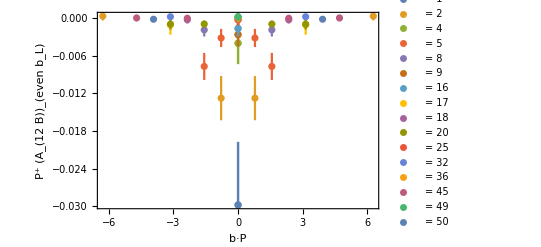

```mathematica
PlotA12B[8]
```

```mathematica
(*Export["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/eta_Pb_bsquare_A12B_err_AllMomentum.h5",Table["Pl-4/eta_"<>ToString[n]<>"_Pb_bsq_A12B_err"->PbbsqA12Bvalueserrbars[n],{n,1,10}],OverwriteTarget->"Append"]*)
```

```mathematica
BIDATEXWriter[M, "/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/test.bidatex"]
```

```mathematica
BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/test.bidatex"]
```

⟨0.617(22)⟩_(RowBox[{)

```mathematica
newDB=NewMemDB[];

Do[MemDBAppend[newDB,{p->-1,bL->bLval,bT->bTval,zta->ztaVal,data->M}],{bLval,{4,6,8}},(*Example values for bL*){bTval,{1,2,3}},(*Example values for bT*){ztaVal,{0.1,0.2,0.3}} (*Example values for zta*)];

BIDATEXWriter[newDB,"/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/tes2t.bidatex"]
```

```mathematica
newDB
```

< -MemDB- {bL,bT,data,p,zta}>

```mathematica
ttt = BIDATEXReader["/Users/hariprashadravikumar/sivers_TMD_PhD_project/save_h5_A12B_A2B/tes2t.bidatex"]
```

< -MemDB- {bL,bT,data,p,zta}>

```mathematica
MemDBGet[ttt,MemDBSelect[ttt,{}],{bL, zta,data}]
```

{{4,0.1,⟨0.617(22)⟩_(RowBox[{)},{4,0.2,⟨0.617(22)⟩_(RowBox[{)},{4,0.3,⟨0.617(22)⟩_(RowBox[{)},{4,0.1,⟨0.617(22)⟩_(RowBox[{)},{4,0.2,⟨0.617(22)⟩_(RowBox[{)},{4,0.3,⟨0.617(22)⟩_(RowBox[{)},{4,0.1,⟨0.617(22)⟩_(RowBox[{)},{4,0.2,⟨0.617(22)⟩_(RowBox[{)},{4,0.3,⟨0.617(22)⟩_(RowBox[{)},{6,0.1,⟨0.617(22)⟩_(RowBox[{)},{6,0.2,⟨0.617(22)⟩_(RowBox[{)},{6,0.3,⟨0.617(22)⟩_(RowBox[{)},{6,0.1,⟨0.617(22)⟩_(RowBox[{)},{6,0.2,⟨0.617(22)⟩_(RowBox[{)},{6,0.3,⟨0.617(22)⟩_(RowBox[{)},{6,0.1,⟨0.617(22)⟩_(RowBox[{)},{6,0.2,⟨0.617(22)⟩_(RowBox[{)},{6,0.3,⟨0.617(22)⟩_(RowBox[{)},{8,0.1,⟨0.617(22)⟩_(RowBox[{)},{8,0.2,⟨0.617(22)⟩_(RowBox[{)},{8,0.3,⟨0.617(22)⟩_(RowBox[{)},{8,0.1,⟨0.617(22)⟩_(RowBox[{)},{8,0.2,⟨0.617(22)⟩_(RowBox[{)},{8,0.3,⟨0.617(22)⟩_(RowBox[{)},{8,0.1,⟨0.617(22)⟩_(RowBox[{)},{8,0.2,⟨0.617(22)⟩_(RowBox[{)},{8,0.3,⟨0.617(22)⟩_(RowBox[{)}}

```mathematica
(*datafor2dGaussianFitbLbTerrors={};
Do[
dataPointErr=MakeErrBars[PlotbLforDiffbTList[[TagbT]]];
Do[
AppendTo[datafor2dGaussianFitbLbTerrors,{{dataPointErr[[All,1]][[TagbL]][[1]],bTlist[[TagbT]],dataPointErr[[All,1]][[TagbL]][[2]]},dataPointErr[[All,2,1]][[TagbL]]}];
,{TagbL,Length[dataPointErr]}];
,{TagbT,Length[bTlist]}];
points=datafor2dGaussianFitbLbTerrors[[All,1]];
errors=datafor2dGaussianFitbLbTerrors[[All,2]];
Print[datafor2dGaussianFitbLbTerrors]

fitbLbLbT=NonlinearModelFit[points,A*Exp[-((alpha*()^2)+(beta*()^2))],{A,alpha, beta},{,},Weights->1/(errors[[All,2]]^2),Method->"LevenbergMarquardt",MaxIterations->10000];
Print["Fitting into   = ",Normal[fitbLbLbT]];
Print["\n             Fit dependence in  space"];
PlotfitbLbT=Show[PlotbL,Table[Plot[fitbLbLbT[x,bT],{x,Min[bLlist],Max[bLlist]},PlotStyle->ColorData[97,"ColorList"][[bT]]],{bT,1,Length[bTlist]}]];
Print[PlotfitbLbT];
Print["\n                 Cast in ,  space"];
FnbdotPbsqre[bp_,b2_]:=(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))];
bsquarelist={1,4,9,16,25};
PlotbLdata= ErrorListPlot[Table[MakeErrBars[PlotbLforDiffbTList[[bT]]],{bT, Length[bTlist]}],FrameLabel->{Style[,Large],Style[,Large]}, Frame->True ,PlotLegends->Table[" = "<>ToString[bTlist[[bT]]],{bT,Length[bTlist]}]];
Cast=Show[PlotbLdata,Table[Plot[FnbdotPbsqre[x,bsq],{x,Min[bLlist],Max[bLlist]}, Frame->True],{bsq,bsquarelist}]];
Print[Cast];
Print[" = ",bsquarelist]
Print["\n                 Fourier transform "];
xFourierTransf[x_, b2_]:= FourierTransform[(A/.fitbLbLbT["BestFitParameters"])*Exp[-((bp^2)*(alpha/.fitbLbLbT["BestFitParameters"]))-(((b2) - (bp^2))*(beta/.fitbLbLbT["BestFitParameters"]))],bp,x];
xFourier=Show[Table[Plot[xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];
Print["\n    Normalize to -integrated Sivers shift, multiply by "];
xFourier=Show[Table[Plot[-x*xFourierTransf[x,bsq],{x,0,1}, AxesLabel->{x,None}],{bsq,bsquarelist}]];
Print[xFourier];*)
```